```mathematica
ep0 = 8.8541878128*10^(−12)
kb = 1.380649*10^(−23)
ee = 1.602*10^(-19)

a = 2*10^(-10)
mp = 1.67262192*10^(-27)
hbar = 1.05457182 *10^(-34)
me = 9.1093837*10^(-31)
ui = 13.6 * ee
```

8.85419×10^-12

1.38065×10^-23

1.602×10^-19

1/5000000000

1.67262×10^-27

1.05457×10^-34

9.10938×10^-31

2.17872×10^-18

8.85419×10^-12

1.38065×10^-23

1.602×10^-19

```mathematica
n[ld_,T_]:= (ep0*kb/(ee^2))*((10^T)/(ld^2))
```

```mathematica
ntau[tau_,T_]:= (1/(Pi*a*a))*((mp/kb)^0.5)*(1/(tau*((10^T)^0.5)))

ni[nn_, T_] := Sqrt[nn*((2*Pi*me*kb*T/(hbar^2))^(3/2))*Exp[(-ui/(kb*T))]]

nitau[tau_, T_]:=ni[ntau[tau,T],T]
```

```mathematica
myl1={Log10[n[1.0,x1]],Log10[n[10^(-2),x1]],Log10[n[10^(-4),x1]],Log10[n[10^(-8),x1]]}
myl2={Log10[nitau[10^(0),x1]],Log10[ni[ntau[10^(-4),x1],x1]]}
myl=Join[myl2]
```

{Log[4763.29 10^x1]/Log[10],Log[4763.29 10^(4+x1)]/Log[10],Log[4763.29 10^(8+x1)]/Log[10],Log[4763.29 10^(16+x1)]/Log[10]}

{Log[2.29046×10^20 √((ⅇ^(-157804./x1) x1^(3/2))/((10^x1)^0.5))]/Log[10],Log[2.29046×10^22 √((ⅇ^(-157804./x1) x1^(3/2))/((10^x1)^0.5))]/Log[10]}

{Log[2.29046×10^20 √((ⅇ^(-157804./x1) x1^(3/2))/((10^x1)^0.5))]/Log[10],Log[2.29046×10^22 √((ⅇ^(-157804./x1) x1^(3/2))/((10^x1)^0.5))]/Log[10]}

```mathematica
Sort[myl]
```

{Log[(8.75886×10^18)/((10^x1)^0.5)]/Log[10],Log[9.09877×10^22 √(-(Exp √x1)/((10^x1)^0.5))]/Log[10]}

```mathematica
Plot[myl,{x1,2,10},PlotRange->{{2,10},{4,32}},PlotLegends->Automatic]
```

General::munfl: Exp[-78895.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72941.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-67823.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
N[n[1.0,1*10^(-3)]]
N[Log10[ntau[10^(-2),10^6]]]
N[ni[10^(20),10^8]]
```

4774.27

General::munfl: 0.0110067 1.×10^-499998 is too small to represent as a normalized machine number; precision may be lost.

Indeterminate

7.73316×10^27

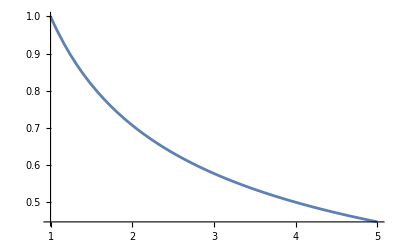

```mathematica
Plot[(1/(x^0.5)),{x,1,5}]
```

```mathematica
n[1.,100000.]
```

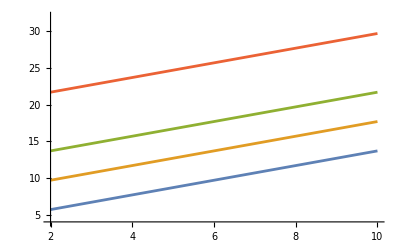

```mathematica
Plot[{Log10[n[1.0,x1]],Log10[n[10^(-2),x1]],Log10[n[10^(-4),x1]],Log10[n[10^(-8),x1]]},{x1,2,10},PlotRange->{{2,10},{4,32}}]
```

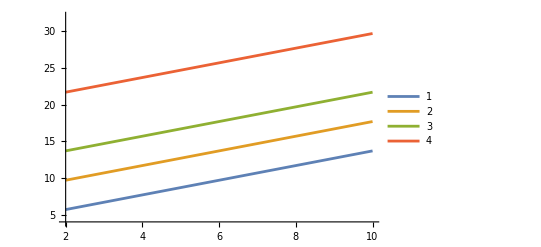

```mathematica
Plot[{Log10[n[1.,x1]],Log10[n[1/10^2,x1]],Log10[n[1/10^4,x1]],Log10[n[1/10^8,x1]]},{x1,2,10},PlotRange->{{2,10},{4,32}},PlotLegends->Automatic]
```

```mathematica
N[Pi]
N[Exp[1]]
```

3.14159

2.71828